Forces on a Submerged Gate

```mathematica
δ=0.25;Δ=1.5;
```

```mathematica
col=RGBColor[0.6,1,0.95];
```

```mathematica
text1[var_,back_]:=Framed[Style[Row@{NumberForm[var,{5,2}]," m"},17],Background->back,FrameStyle->None,FrameMargins->Tiny];
```

```mathematica
text2[var_,back_]:=Framed[Style[Row@{NumberForm[N@var/1000,{5,1}]," kN"},18],Background->back,(*FrameStyle->None,*)FrameMargins->Small];
```

```mathematica
Manipulate[
Module[{W,γ,θ,h,d2,w2,w1,d,A,hc,FR,yc,Ixc,yR,FA,func,dist,x,y,scale,labels},
W=W0*1000;γ=9800;(*N/m3*)

θ=35°;
h=2.5;d2=h*Sin[θ];w2=h*Cos[θ];w1=1.1;d=d1-d2;(*m*)

A=h*w2;(*m2*)
hc=d+0.5*h*Sin[θ];(*m*)
FR=γ*hc*A;

yc=0.5*h+d/Sin[θ];
Ixc=1/12*w2*h^3;
yR=yc+Ixc/(yc*A);

FA=fa/.Quiet@Solve[FR*(yR-d/Sin[θ])+W*0.5*h*Sin[θ]-fa*h==0,fa][[1]];


func[z_]:=d2/(w1-(w1+w2))*(z-w1)+d2;

dist=√((x[4]-(w1+w2))^2+(y[4]-0)^2);
x[1]=w1+w2-(0.333*dist)*Cos[θ];y[1]=(0.333*dist)*Sin[θ];(*resultant force location*)
x[2]=w1+0.5*h*Cos[θ];y[2]=d2-0.5*h*Sin[θ];(*weight location*)
x[3]=w1+w2;y[3]=0;(*applied force*)
x[4]=Quiet@(z/.Solve[func[z]==d1,z][[1]]);y[4]=d1;

scale[F_]:=Rescale[F,{-25000,114547}];

(*distance[p1_,p2_]:=√((p1[[1]]-p2[[1]])^2+(p1[[2]]-p2[[2]])^2);*)

labels={PointSize@0.017,
(*water height*)
Line[{{0.25*w1,0},{0.25*w1,d1}}],Text[Style["—",17],{0.25*w1,#}]&/@{0,d1},Text[text1[d1,col],{0.25*w1,0.5*d1}],
(*hinge height*)
Line[{{w1,0},{w1,d2}}],Text[Style["—",17],{w1,#}]&/@{0,d2},Text[text1[d2,col],{w1,0.5*d2}],
(*weight length*)
Line[{{w1+δ,d2+δ},{x[2]+δ,y[2]+δ}}],
Text[Rotate[Style["—",17],90°-θ],#]&/@{{w1+δ,d2+δ},{x[2]+δ,y[2]+δ}},
Text[text1[0.5*h,White],{w1+x[2]+2*δ,d2+y[2]+2*δ}/2],
(*resultant force length*)
Line[{{x[1]+2*δ,y[1]+2*δ},{w1+w2+2*δ,2*δ}}],
Text[Rotate[Style["—",17],90°-θ],#]&/@{{x[1]+2*δ,y[1]+2*δ},{w1+w2+2*δ,2*δ}},
Text[text1[0.33*dist,White],{x[1]+w1+w2+4*δ,y[1]+4*δ}/2],
(*gate length*)
Line[{{w1+3*δ,d2+3*δ},{w1+w2+3*δ,3*δ}}],Line[{w1+3*δ+#,d2+3*δ+#}&/@{-0.05,0.05}],Line[{w1+w2+3*δ+#,3*δ+#}&/@{-0.05,0.05}],
Text[text1[h,White],{2*w1+w2+6*δ,d2+6*δ}/2]
};

Graphics[{Arrowheads@0.05,
Line[{{#,-0.25},{#+0.25,0}}]&/@Range[0,w1+w2-0.25,0.25],

{col,Polygon[{{w1,d1},{0,d1},{0,0},{w1+w2,0},{w1,d2}}]},

{Thickness@0.02,CapForm@None,Line[{{0,3},{0,0},{w1+w2,0}}]},
{Thick,Line[{{w1,3},{w1,d2}}]},
{Thickness@0.03,GrayLevel@0.4,CapForm@"Round",Line[{{w1,d2},{w1+w2,0}}]},
{PointSize@0.055,Point@{w1,d2},PointSize@0.04,White,Point@{w1,d2}},

Circle[{w1+w2,0},0.5,{180°,180°-θ}],
Text[Style[θ,17],{w1+w2-0.5,0},{1,-2}],

If[label,labels],

(*resultant force*)
{Thick,Purple,Arrow[{{x[1]-scale[FR]*Cos[90°-θ],y[1]-scale[FR]*Sin[90°-θ]},{x[1],y[1]}}],PointSize@0.02,Point@{x[1],y[1]},
Text[text2[FR,White],{x[1]-scale[FR]*Cos[90°-θ],y[1]-scale[FR]*Sin[90°-θ]},{0,1}]},

(*gate weight*)
{Thick,Blue,Arrow[{{x[2],y[2]},{x[2],y[2]-scale[W]}}],PointSize@0.02,Point@{x[2],y[2]},
Text[text2[W,White],{x[2],y[2]-scale[W]},{0,1.2}]},

(*applied force*)
{Thick,RGBColor[0,0.6,0],Arrow[{{x[3]+scale[FA]*Cos[90°-θ],y[3]+scale[FA]*Sin[90°-θ]},{x[3],y[3]}}],PointSize@0.02,Point@{x[3],y[3]},
Text[text2[FA,White],{x[3]+scale[FA]*Cos[90°-θ],y[3]+scale[FA]*Sin[90°-θ]},{0,-1}]},
},ImageSize->{600,425},PlotRange->{{0,4},{-0.5,3}}]
],
Grid@{{
Control[{{d1,2.7,"water height (m)"},1.5,3,0.1,Appearance->"Labeled",ImageSize->Small}],
Control[{{W0,5,"gate weight (kN)"},1.5,5,0.1,Appearance->"Labeled",ImageSize->Small}],
Control[{{label,False,"show labels"},{True,False}}]
}},
SaveDefinitions->True]
```

```mathematica
Module[{p1,p2},
p1={2.218,1.501};
p2={3.638,0.5039};
√((p1[[1]]-p2[[1]])^2+(p1[[2]]-p2[[2]])^2)
]
```

1.73511

```mathematica
labels={
(*water height*)
Line[{{0.25*w1,0},{0.25*w1,d1}}],Line[{{0.25*w1-0.2*δ,#},{0.25*w1+0.2*δ,#}}]&/@{0,d1},
Text[text1[d1,col],{0.25*w1,0.5*d1}],
(*hinge height*)
Line[{{w1,0},{w1,d2}}],Line[{{w1-0.2*δ,#},{w1+0.2*δ,#}}]&/@{0,d2},
Text[text1[d2,col],{w1,0.5*d2}],
(*weight length*)
Line[{{w1+δ,d2+δ},{x[2]+δ,y[2]+δ}}],Line[{w1+δ+#,d2+δ+#}&/@{-0.05,0.05}],Line[{x[2]+δ+#,y[2]+δ+#}&/@{-0.05,0.05}],
Text[text1[0.5*h,White],{w1+x[2]+2*δ,d2+y[2]+2*δ}/2],
(*resultant force length*)
{Line[{{x[1]+2*δ,y[1]+2*δ},{w1+w2+2*δ,2*δ}}],Line[{x[1]+2*δ+#,y[1]+2*δ+#}&/@{-0.05,0.05}],
Text[text1[0.33*dist,White],{w1+w2+x[1]+4*δ,y[1]+4*δ}/2]},
(*gate length*)
Line[{{w1+3*δ,d2+3*δ},{w1+w2+3*δ,3*δ}}],Line[{w1+3*δ+#,d2+3*δ+#}&/@{-0.05,0.05}],Line[{w1+w2+3*δ+#,3*δ+#}&/@{-0.05,0.05}],
Text[text1[h,White],{2*w1+w2+6*δ,d2+6*δ}/2],
(*water height*)
Line[{{w1+0.75*δ,d2},{w1+0.75*δ,d1}}],Line[{{w1+0.55*δ,#},{w1+0.95*δ,#}}]&/@{d2,d1},
Text[text1[d1-d2,White],{w1+0.75*δ,d2+0.5*(d1-d2)}]
};
```

A gate, which is hinged at the top, is submerged under water, and an applied force holds the gate closed. Set the water height and the gate weight with sliders. Check the "show labels" box to display distances. This Demonstration displays the applied force needed to keep the gate closed.





This Demonstration determines the magnitude of the applied force needed to keep a gate that is w_2 meters wide and d_1 meters tall, closed (see Figure 1).

The magnitude of the resultant force is found by summing the differential forces over the entire surface:

F_R=∫_A γ hⅆA=∫_A γ y sin θⅆA,

where h=y sin θ is the vertical distance from the fluid surface to the centroid center (m), y is the y-coordinate of the height along the diagonal (m), F_R is the resultant force (N), A=h w_2 is area (m^2), w_2 is the width of the gate (m), θ is angle (degrees), and γ is the specific weight of water (N/m^3).

For constant θ and γ:

F_R=γ sin θ ∫_A yⅆA.

The integral ∫_A yⅆA is the first moment of the area with respect to the x-axis, so:

∫_A yⅆA=y_c A,

where y_c=h/2+d/sin θ is the y-coordinate of the centroid of area A measured from the x-axis which passes through 0 (m), h is the diagonal length of the gate (m), d=d_1-d_2 is the vertical height from the top of the gate to the top of the fluid (m), d_1 is the fluid height (m), and d_2 is the height of the gate (m). The resultant force can be written as:

F_R=γ y_c sin θ A=γ h_c A,

where h_c is the vertical distance from the fluid surface to the centroid of area (m).

The y-coordinate y_R of the resultant force can be found by summation of moments around the x-axis:

F_R y_R=∫_A yⅆF=∫_A γ y^2 sin θⅆA,

therefore since F_R=γ y_c sin θ A, y_R=(∫_A y^2 ⅆA)/(y_c A).

The integral in the numerator is the second moment of the area (moment of inertia) I_x, with respect to an axis formed by the intersection of a plane containing the surface and the free surface (x-axis). Thus we can write:

y_R=I_x/(y_c A).

The parallel axis theorem is used to define I_x=I_xc+A y_c^2 where I_xc is the second moment of the area with respect to an axis passing through its centroid and parallel to the x-axis, thus:

y_R=I_xc/(y_c A)+y_c,

where I_xc=1/12 w_2 h.

A moment balance is done to determine the applied force that keeps the gate closed:

∑M=0=F_R (y_R-d/sin θ)+W h/2 sin θ-F_A h,

rearranging to solve for F_A:

F_A=(F_R (y_R-d/sin θ)+W h/2 sin θ)/h,

where W is the weight of the gate (N), and F_A is the applied force (N).

Figure 1

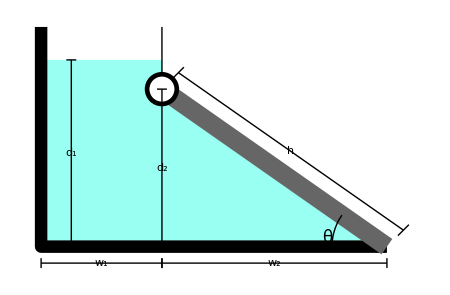

Reference

[1] W.W. Huebsch, B.R. Munson, T.H. Okiishi, and D.F. Young, Fundamentals of Fluid Mechanics, 6th ed., New Jersey: Jon Wiley & Sons, 2009 pp 58-60.

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

chemical engineering

fluid dynamics

gate

Contributed by: Rachael L. Baumann

Additional contributions by: John L. Falconer

(University of Colorado Boulder, Department of Chemical and Biological Engineering)